Greatest eigenvector:

{-0.698703,0.715412}

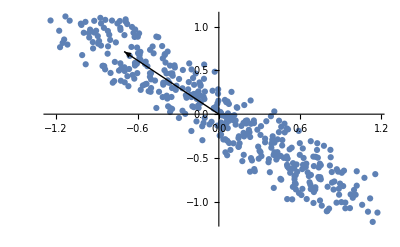

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../assets/oja_unsupervised/"];
data=Import["data.txt","Table"];

(* Normalize data to zero mean *)
DataMean=Mean[data];
data=Map[Function[x,x-DataMean],data];

(* Calculate covariance matrix of data *)
cov=Table[0,{2},{2}];
Do[
cov+=(Transpose[{vec}].{vec}),
{vec,data}
];
cov/=Length[data];

(*
Print["Covariance matrix"];
MatrixForm[cov]
*)

eigenvecs=Eigenvectors[cov];
ind=Ordering[Eigenvalues[cov],-1];

Print["Greatest eigenvector:"]
vec=eigenvecs[[ind]][[1]]

Show[
ListPlot[data],
Graphics[Arrow[{{0,0},vec}]]
]
```